# Level 2 Certification Project

## Benjamin Ciotti, benjaminciotti@boisestate.edu February 12, 2026

The goal here is to to use neural networks to predict NFL outcomes.  There are many types of outcomes that one can try to predict such as which team will win, how much they will win by, whether they will cover the spread (i.e. win by more than anticipated), what the (combined) total number of points scored will be, and (in my case) whether the combined total number of points will be less than anticipated.  In the terminology of sports betting I am attempting to predict whether the under will hit.

There is a clear application of such prediction models, namely profitable sports betting.  Moreover these techniques may be modified to predict outcomes in other sports (which may be of particular relevance in the NFL off-season).

## Data Preprocessing

My dataset on NFL game outcomes, nfl_full.csv, was found on Kaggle at https://www.kaggle.com/datasets/tobycrabtree/nfl-scores-and-betting-data.  It contains data on 14358 NFL games going back to the 1960s, and the data included point totals, spreads, dates, years, which week of the season a game was in, where it was played, what the weather conditions were, whether it was a playoff game, who the home team was, who the favorite was, and (crucially) spreads (how many points the favorite is expected to win by), over/unders (the anticipated total number of points), and how many points each team in-fact scored.  

nfl_teams.csv is a supplemental spreadsheet of team names and their associated abbreviations and is from the same Kaggle page.

```mathematica
(*Run the following to import the two data files nfl_full.csv and nfl_teams.csv if they are in the same directory as the notebook*)
full=Import[FileNameJoin[{NotebookDirectory[],"nfl_full.csv"}],"CSV"];
teams=Import[FileNameJoin[{NotebookDirectory[],"nfl_teams.csv"}],"CSV"];
```

```mathematica
(*Alternately the following can be run to download copies from my Google drive*)

(*
full=Import["https://drive.google.com/uc?export=download&id=1H34aLzlmm5MecSjYnPbWGODBr2g9ehhD","CSV"];
teams=Import["https://drive.google.com/uc?export=download&id=14_H8H4T6hJxtrAAvF6OZ70uDOCyhqZ8L", "CSV"];
*)
```

Let’s visualize our data:

```mathematica
Dataset[full]
```

Dataset[<>]

We see we have 14359 rows (including the header) and 17 columns of data.

A lot of data is missing.  To deal with this I first determine which columns are missing the most data:

```mathematica
missingCounts=Map[Count[#, _Missing]&, Transpose[full]];
headers=First[full];
Transpose@Dataset@Prepend[{missingCounts},headers]
```

We see the last two columns have significantly more missing values than the other columns, so let’s drop those:

```mathematica
dropCols=full[[All, 1;;15]];
```

Now let’s delete all the rows that have missing entries:

```mathematica
dropMissing=DeleteMissing[dropCols, 1,Infinity];
Dimensions@dropMissing
```

{10546,15}

We see we still have 10,545 rows of game data so there is still plenty to train on.  There would have been far fewer complete rows had I not first dropped those last two columns that were missing a lot of entries. 

I want to replace all the team names with their three-letter abbreviations (or team_id) for consistency, since my dataset uses the abbreviations to label favorites.  

Note: I’m not 100% sure this is a good idea (and a longer project would compare my results to those obtained by skipping this step).  The issue is that teams occasionally change names or cities, and in my analysis I will be treating them as the same team when that happens.  So for example the LA Rams and the St. Louis Rams will both be assigned the abbreviation LAR.  The Las Vegas Raiders and the Los Angeles Raiders and the Oakland Raiders are all assigned LVR.  The Houston Oilers, Tennessee Oilers, and Tennessee Titans are all assigned TEN.

```mathematica
(*Here is my teams dataset*)
Dataset@teams
```

```mathematica
(*And here I create my association sending each team to its abbreviation:*)
teamMap=Association[Rule@@@teams[[2;;,{1,3}]]]
```

<|Arizona Cardinals→ARI,Atlanta Falcons→ATL,Baltimore Colts→IND,Baltimore Ravens→BAL,Boston Patriots→NE,Buffalo Bills→BUF,Carolina Panthers→CAR,Chicago Bears→CHI,Cincinnati Bengals→CIN,Cleveland Browns→CLE,Dallas Cowboys→DAL,Denver Broncos→DEN,Detroit Lions→DET,Green Bay Packers→GB,Houston Oilers→TEN,Houston Texans→HOU,Indianapolis Colts→IND,Jacksonville Jaguars→JAX,Kansas City Chiefs→KC,Las Vegas Raiders→LVR,Los Angeles Chargers→LAC,Los Angeles Raiders→LVR,Los Angeles Rams→LAR,Miami Dolphins→MIA,Minnesota Vikings→MIN,New England Patriots→NE,New Orleans Saints→NO,New York Giants→NYG,New York Jets→NYJ,Oakland Raiders→LVR,Philadelphia Eagles→PHI,Phoenix Cardinals→ARI,Pittsburgh Steelers→PIT,San Diego Chargers→LAC,San Francisco 49ers→SF,Seattle Seahawks→SEA,St. Louis Cardinals→ARI,St. Louis Rams→LAR,Tampa Bay Buccaneers→TB,Tennessee Oilers→TEN,Tennessee Titans→TEN,Washington Commanders→WAS,Washington Football Team→WAS,Washington Redskins→WAS|>

```mathematica
(*Now I replace the team names with their abbreviations and fix the header*)
namesToIds=ReplacePart[#, {5->teamMap[#[[5]]], 8->teamMap[#[[8]]]}]&/@dropMissing;
{namesToIds[[1,5]]="team_home_id",namesToIds[[1,8]]="team_away_id"};
```

We are interested in whether the total number of points scored is less than the “over_under_line” that is set by the bookies so let’s append a column containing a Boolean of whether that was the case. 

Note: An alternate approach would be to use True or False symbols, or “True” or “False” strings, instead of 0s and 1s.  I’ll go with integer 0s and 1s but in a longer analysis I would try the other approaches and compare the results.

```mathematica
withUnder=Map[Append[#, Boole[Total[#[[6;;7]]]<ToExpression[#[[11]]]]]&,namesToIds];
(*and label the column "over_hit":*)
withUnder[[1,-1]]="under_hit";
```

```mathematica
(*It can be determined that 6 rows have null over_under_lines so let's delete those:*)
Dimensions[withUnder]
noNulls=Select[withUnder,ToExpression[#[[11]]]=!=Null &];
Dimensions[noNulls]
```

{10546,16}

{10540,16}

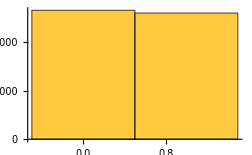

0.494639

```mathematica
(*We see that unders hit about 49.5% of the time:*)
Histogram[noNulls[[2;;,-1]]]
underHitProbability=N@Mean[noNulls[[2;;,-1]]]
```

```mathematica
(*For comparison overs hit about 48.7% of the time and over/unders are a "push" (i.e. exactly as predicted) about 1.85% of the time. This is infrequent because the over_under_line typically ends in .5 rendering it impossible for the total points to equal it, and even if the over_under_line is an integer it is still unlikely that the total points scored to end up equalling it exactly.*)
overHitProbability=N@Mean[Boole[Total[#[[6;;7]]]>ToExpression[#[[11]]]]&/@noNulls[[2;;]]]
pushProbability=N@Mean[Boole[Total[#[[6;;7]]]==ToExpression[#[[11]]]]&/@noNulls[[2;;]]]
```

0.486858

0.0185027

So the raw win rate for unders is about 49.5%, but if we condition upon the bet not resulting in a push (wherein the bookie returns your money to you so there was effectively no bet) we can compute the actual win rate for unders as underHitProbability/(overHitProbability+underHitProbability)≈50.4%.  Similarly the actual win rate for overs is overHitProbability/(overHitProbability+underHitProbability)≈49.6%.  

We see that unders are more likely to hit than overs so it makes more sense to bet on unders than overs.  (Fun fact: I had originally written this assignment to predict when to bet on overs but rewrote it to bet on unders in light of this fact.)

It can be shown that if an outcome happens with a probability P>50%, then an optimal no-additional-information betting strategy is to bet on its occurrence 100% of the time (and if P<50% then bet against it 100% of the time).  So knowing only that the actual win rates for unders is 50.4%, we could simply bet on the under 100% of the time and win 50.4% of decided (non-push) games. If we include pushes this means we want bets on the under to win more than 50.4/(50.4+ 49.6+1.85)≈49.6% of the time (i.e. we want to beat the underHitProbability).

But wait - if we are betting in the real world then we have to take the “vig” into account.  Real-world bookies don’t offer 50:50 odds on over/unders.  Rather they typically offer bets at “-110,” meaning you have to risk $110 to win $100.  It can be shown that, in the absence of pushes, this means you have to win over 110/210≈52.4% of such bets in order to be profitable.  If we assume that 1.85% of bets on the over/under are pushes then this falls to 110*(1-.0185)/210≈51.4%.  So this will be my target accuracy rate.  Basically I want my predictions to be correct more than 51.4% of the time (or equivalently my error rate to be less than 48.6%).

```mathematica
(* Let's check what types of data are in each column:*)
Dataset@Map[Function[column,{column[[1]],Tally[Head /@ column[[2 ;;]]]}],Transpose[noNulls]]
```

I think it’s probably a good idea to coerce some of the data.  The schedule_date values are strings that look like “1/14/1968” and I would like to coerce them into numeric form.  I do so by converting the dates to absolute times (which are the number of seconds since January 1 1900):

```mathematica
(*define function which takes in a date string and spits out and absolute time*)
convertDateToAbsoluteTime[dateString_]:=AbsoluteTime[DateObject[{dateString,{"Month","Day","Year"}}]];
(*Apply to my dataset:*)
absoluteTime=ReplacePart[#, 1->convertDateToAbsoluteTime[#[[1]]]]&/@Rest[noNulls];
(*Add back the header:*)
absoluteTime=Prepend[absoluteTime, noNulls[[1]]];
```

Now I remove playoff games.  This is because they don’t have an integer value for the week and I don’t want to deal with this so I will avoid such cases by just deleting them from my data.  

Note: A more sophisticated approach might be to replace them with a week number but this would take some effort to accurately implement being as, e.g., the NFL has changed the number of weeks in a season over the years.

```mathematica
(*Deleting playoff games:*)
noPlayoff=Select[absoluteTime, #[[4]]=!=True&] ;
```

```mathematica
(*The schedule_playoff column is now meaningless since every value is False so we may as well drop that entire column*)
noPlayoffCol=Drop[#, {4}]&/@noPlayoff;
```

Now I coerce schedule_week from string to integer, over_under_line to real, and stadium_neutral to Boolean:

```mathematica
coerced=Map[
ReplacePart[#,{3->ToExpression[#[[3]]], 10->N[ToExpression[#[[10]]]],12->Boole[#[[12]]]}] &,
  Rest[noPlayoffCol]
];
(*adding back the header:*)
coerced=Prepend[coerced, noPlayoffCol[[1]]];
```

Finally, and this is important, I delete the columns containing the number of points scored by each team.  This is information that would not be known prior to the occurrence of a game so we should not be taking it as an input to be used for the purpose of predicting future games.   

Note: I am hesitant to do this because I’m losing information and I would prefer to train on this information without requiring it as an input for making predictions.  Perhaps the way to do this is to train my net with these columns as additional outputs and to minimize losses across multiple outputs but at the time of writing this I haven’t figured out how to effectively implement this.

```mathematica
(*Dropping the team score columns:*)
noPts=Drop[#, {5,6}]&/@coerced;
```

```mathematica
(*Let's check how many games we have left in our dataset*)
Dimensions[noPts]
```

{10322,13}

### Now let’s split our data into a training (80%) and testing (20%) set:

```mathematica
(*80% of 10322 is roughly 8300 so let's use that as the size of our training set and reserve the rest for testing.  First I set a seed for reproducibility:*)
SeedRandom[42];
{train,test}=TakeDrop[RandomSample[Rest[noPts]], 8300];
(*and do a quick check of dimension*)
Dimensions/@{train, test}
```

{{8300,13},{2021,13}}

```mathematica
(*Now separate train and test into inputs and outputs*)
trainInput=train[[All,;;12]];
testInput=test[[All,;;12]];
trainOutput=train[[All, 13]];
testOutput=test[[All,13]];
```

## Encoding

I use FeatureExtraction to define a FeatureExtractorFunction that will take my (training) input data and convert it to numeric form. 

Note: I tried various ways of doing this including doing it only on certain components of the input data, specifying whether I wanted the results to be indicator or standardized vectors, composing multiple extractors, and after all that it was simply default FeatureExtraction[] parameters that yielded the most effective results:

```mathematica
(*Train my FeatureExtractorFunction:*)
fe=FeatureExtraction[trainInput]
```

FeatureExtractorFunction[…]

```mathematica
(*Perform the extraction on my training and testing input data*)
trainInputFE=fe[trainInput];
testInputFE=fe[testInput];
```

## Defining and Training the Net

```mathematica
(*Initialize the net:*)
net=NetModel[{"Self-Normalizing Net for Numeric Data", "TaskType"->"Regression","DropoutProbability"->0.01, "Depth"->7, "Width"->35}]
```

NetChain[…]

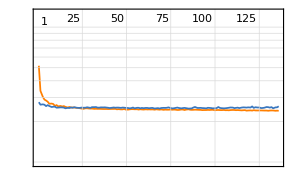
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5304  rounds:136  time:11s  examples/s:99598
data | ,,  training examples:7800  validation examples:600  processed examples:1060800  skipped examples:0
method | ,,  ADAMoptimizer  batch size200CPU
round | ,,  loss:2.4×10^-1
validation | ,,  loss:2.59×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*Setting a seed and training the net:*)
SeedRandom[42];
netTrained=NetTrain[net,trainInputFE->trainOutput,All, ValidationSet->Scaled[0.07],Method->{"ADAM", "L2Regularization"->.001},BatchSize->200,TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->50|>]
```

I tested various values of DropoutProbability, Depth, Width, Method, L2Regularization, TrainingStoppingCriterion, and BatchSize by altering them one at a time to find the ideal combination of parameters for my net and training.

## Evaluating Net Performance

```mathematica
(*Let's take a look at some of our predictions (and make sure they aren't all the same for one).  I view each of these as the probability that I should bet on the under, so predictions above 50% round to 1 and correspond to predictions on betting on the under:*)
predictions=netTrained["TrainedNet"][testInputFE];
predictions[[1;;20]]
```

{0.486785,0.530725,0.427202,0.418401,0.458811,0.498377,0.533679,0.451179,0.467226,0.498427,0.526081,0.376231,0.483221,0.56231,0.444771,0.452558,0.510469,0.546624,0.500814,0.357168}

The following gives the proportion of accurate predictions i.e. the accuracy rate of my model.  This is what I hope to be above 51.4%.

```mathematica
N@Mean@Boole@MapThread[Equal,{Round[predictions],testOutput}]
```

0.540327

In this randomization my accuracy is an impressive 54%, well above the target of 51.4%.  That said, not all randomizations of train and test data may yield models that perform as well.

In a future project I would write a loop that resamples and retrains so as to get a better accuracy estimate (and see the supplemental section for an implementation of something like this) and moreover program the loops to optimize over different hyperparameter values.

### Now let's compare to the accuracy of models generated by Predict[] :

```mathematica
pred=Predict[trainInput->trainOutput, RandomSeeding->42]
(*Note: Setting RandomSeeding apparently does not guarantee reproducibility of Predict training but that was my goal.*)
```

PredictorFunction[…]

```mathematica
(*The accuracy rate of the Predict function generated *)
N@Mean@Boole[MapThread[Equal,{Round[pred[testInput]], testOutput}]]
```

0.534884

Compare this to the 54.03% accuracy achieved by my net. 

Another measure of the accuracy of predictions is the RMSE (also called “StandardDeviation” in the context of regression measurements) and we want this to be as low as possible. 

The RMSE of my net’s predictions can be found as

```mathematica
(Mean[(predictions-testOutput)^2])^.5
(*This is equivalent to 
NetMeasurements[netTrained["TrainedNet"], testInputFE->testOutput, "StandardDeviation"]
*)
```

0.499456

Compare this to the RMSE of the Predict[] predictions:

```mathematica
(Mean[(pred[testInput]-testOutput)^2])^.5
(*Note this is the same as
PredictorMeasurements[pred,testInput->testOutput, "StandardDeviation" ]
*)
```

0.499385

Let’s compare this to the RMSE of all the various methods of Predict[].  Warning: This cell could take a long time to execute and skipping it is may be advisable.

```mathematica
ReverseSort@Dataset@AssociationMap[PredictorMeasurements[Predict[trainInput->trainOutput,Method->#],testInput->testOutput,"StandardDeviation"]&,{"RandomForest","DecisionTree","GradientBoostedTrees","NearestNeighbors","LinearRegression","GaussianProcess", "NeuralNetwork"}]
```

Depending on randomization it appears that by the RMSE metric my net outperforms about half of the Predict methods. 

Let’s specifically compare Predict’s NeuralNetwork to our net:

```mathematica
predNN=Predict[trainInput->trainOutput, Method->"NeuralNetwork", RandomSeeding->42]
(*Again RandomSeeding may not guarantee reproducibility*)
```

PredictorFunction[…]

```mathematica
(*The RMSE of the Predict Neural Net:*)
PredictorMeasurements[predNN,testInput->testOutput, "StandardDeviation" ]
(*The accuracy of the Predict Neural Net:*)
N@Mean@Boole[MapThread[Equal,{Round[predNN[testInput]], testOutput}]]
```

0.499999

0.499258

In this randomization my net has both a lower RMSE and a better accuracy than Predict’s neural net.

## Applying my models to the Super Bowl:

I looked up the date, teams, spread, over_under_line, stadium (which was neutral), weather_temperature, and weather_wind_mph for Super Bowl XV (which occurred last weekend as I write this).  I put the schedule_week as 18 since the season was 17 weeks long).

```mathematica
sb={convertDateToAbsoluteTime["2/8/2026"],2026,18, "NE","SEA", "SEA", -4.5, 46.5, "Levi's Stadium", 1, 60, 7.5}
```

{3.9795×10^9,2026,18,NE,SEA,SEA,-4.5,46.5,Levi's Stadium,1,60,7.5}

I FeatureExtracted and plugged it into my net:

```mathematica
netTrained["TrainedNet"][fe[sb]]
```

0.410871

This shows that we should not bet on the under, and this prediction was incorrect as the true point total was 29+13=42 which was indeed under the over/under line of 46.5. 

Let’s check the predictions of the Predict models:

```mathematica
pred[sb]
predNN[sb]
```

0.631879

0.509813

In my randomization it appears that both the LinearRegression and NeuralNet models generated by Predict correctly suggest betting on the under. 

This may suffice for Level 2 Certification but I’ve included some additional work in the supplemental sections that follow.
-Ben Ciotti

## Supplement 1: An alternate approach using a classification net

I mentioned previously that perhaps I should be using a classification net on True or False outcomes instead of integer 1’s or 0’s.  Here I try that approach to see if it works better.

```mathematica
(*Replace the 0 and 1 outputs with False and True symbols in the trainOutput and testOutput sets*)trainOutputTF=Replace[trainOutput,{1->True,0->False},{1}];
testOutputTF=Replace[testOutput,{1->True,0->False},{1}];
```

```mathematica
(*Define my decoder for the True and False classes:*)
dec=NetDecoder[{"Class", {True, False}}];
```

```mathematica
(*Define my net, using parameter values established through testing*)
netTF=NetModel[{"Self-Normalizing Net for Numeric Data", "DropoutProbability"->.01, "Depth"->9, "Width"->25}]
```

NetChain[…]

I tried replacing some layers in my net, but this did not improve performance, hence I do not include the code.

```mathematica
(*Train the net:*)
trainedNetTF=NetTrain[NetReplacePart[netTF,"Output"->dec],trainInputFE->trainOutputTF,All, ValidationSet->Scaled[0.05],BatchSize->1000]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4528  rounds:566  time:18s  examples/s:263516
data | ,,  training examples:8000  validation examples:1000  processed examples:4528000  skipped examples:0
method | ,,  ADAMoptimizer  batch size1000CPU
round | ,,  loss:4.55×10^-1  error:20.6%
validation | ,,  loss:9.56×10^-1  error:43.8%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*Compute the accuracy of my net, evaluated on the test set:*)
N@Mean@Boole[MapThread[Equal,{trainedNetTF["TrainedNet"][testInputFE], testOutputTF}]]
(*Equivalently this can be found as
ClassifierMeasurements[trainedNetTF["TrainedNet"], testInputFE->testOutputTF]["Accuracy"]
*)
```

0.514597

While 51.46% is not bad, we see that my regression net was more accurate.

We can visualize classifier properties (such as the ConfusionMatrix) using ClassifierMeasurements:

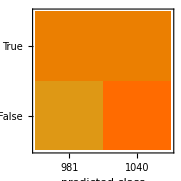
Classifier Measurements
Classifier method | Net
Number of test examples | 2021
Accuracy | (51.51.1) %
Accuracy baseline | (50.51.1) %
Geometric mean of probabilities | 0.36 ± 0.0084
Mean cross entropy | 1.02 ± 0.023
Single evaluation time | 2.74 ms/example
Batch evaluation speed | 29.9 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[trainedNetTF["TrainedNet"], testInputFE->testOutputTF]
```

### Improving the accuracy of the classifier net

The following code was taken from the section of https://resources.wolframcloud.com/NeuralNetRepository/resources/Self-Normalizing-Net-for-Numeric-Data/ on “Improving accuracy of the classifier net” and the idea is to run multiple trainings and create an ensemble network which averages the outputs of the trained nets:

```mathematica
ensembleNet[n_]:=Module[{ens},ens=Table[NetTrain[NetReplacePart[netTF,"Output"->dec],trainInputFE->trainOutputTF,ValidationSet->Scaled[0.05],MaxTrainingRounds->100,RandomSeeding->RandomInteger[10^6]+n],{i,1,n}];
NetGraph[{Sequence@@ens,TotalLayer[],ElementwiseLayer[#/N@n&]},{NetPort["Input"]->Range[n]->n+1->n+2},"Output"->dec]]
```

This sets our ensemble classifier net to be the average of 4 trainings:

```mathematica
n=4;
ensTrained=ensembleNet[n]
```

NetGraph[…]

```mathematica
(*Compute the accuracy of our ensemble net*)
N@Mean@Boole[MapThread[Equal,{ensTrained[testInputFE], testOutputTF}]]
(*Equivalently this can be computed as
accensemble=ClassifierMeasurements[ensTrained,testInputFE->testOutputTF,"Accuracy"]
*)
```

0.523503

```mathematica
(*For what it's worth we can check the accuracy of the 4 nets that our ensemble net was comprised of:*)Table[ClassifierMeasurements[NetReplacePart[NetExtract[ensTrained,i],"Output"->dec],testInputFE->testOutputTF,"Accuracy"],{i,1,n}]
```

{0.525977,0.514102,0.52004,0.517071}

Maybe a good strategy would be to select the most accurate of these 4 nets to use as my model.

## Supplement 2: Averaging my regression nets

I can average together multiple regression nets in much the way that I created an averaging ensemble of classifier nets:

```mathematica
ensembleNetReg[n_]:=Module[{ens},ens=Table[NetTrain[net,trainInputFE->trainOutput,ValidationSet->Scaled[0.07],MaxTrainingRounds->100,RandomSeeding->RandomInteger[10^6]+n],{i,1,n}];
NetGraph[{Sequence@@ens,TotalLayer[],ElementwiseLayer[#/N@n&]},{NetPort["Input"]->Range[n]->n+1->n+2}]]
```

```mathematica
(*Train 4 nets*)
```

```mathematica
n=4;
ensTrainedReg=ensembleNetReg[n]
```

NetGraph[…]

```mathematica
(*Compute accuracy of the ensemble net:*)
N@Mean@Boole[MapThread[Equal,{Round[ensTrainedReg[testInputFE]], testOutput}]]
```

0.526967

```mathematica
(*Compare accuracy of the 4 comprising nets:*)
Table[N@Mean@Boole[MapThread[Equal,{Round[NetExtract[ensTrainedReg,i][testInputFE]], testOutput}]],{i,1,n}]
```

{0.504206,0.522019,0.507175,0.517566}

## Supplement 3: What would these nets predict for the Super Bowl?

Here I test new nets that I defined in Supplement 1 and Supplement 2 on their Super Bowl prediction:

```mathematica
(*My averaged classifier net ensemble:*)
ensTrained[fe[sb]]
```

False

```mathematica
(*The 4 nets that comprise the ensemble on their individual predictions:*)
Table[NetReplacePart[NetExtract[ensTrained,i],"Output"->dec][fe[sb]],{i,1,n}]
```

{False,False,True,True}

```mathematica
(*My averaged regression net:*)
ensTrainedReg[fe[sb]]
```

0.594339

```mathematica
(*The 4 nets that comprise the regression ensemble net*)
Table[NetExtract[ensTrainedReg,i][fe[sb]],{i,1,n}]
```

{0.642712,0.522968,0.668698,0.542975}

Results seem to vary with randomization but it appears that most of these correctly predict the under for the Super Bowl.